```mathematica
SOI=Import["/users/pp/git/context/Mathematica/SOIM/data/soi.txt", "table"];
TSID=Import["/users/pp/git/context/Mathematica/SOIM/data/tsi.txt", "table"];
QBO=Import["/users/pp/git/context/Mathematica/SOIM/data/qbo20.txt", "table"];
QBO70=Import["/users/pp/git/context/Mathematica/SOIM/data/qbo.txt", "table"];
CW=Import["/users/pp/git/context/Mathematica/SOIM/data/cw.txt", "table"];
CW1=Import["/users/pp/git/context/Mathematica/SOIM/data/cw1_1930.txt", "table"];
CW0=Import["/users/pp/git/context/Mathematica/SOIM/data/cw1.txt", "table"];
NINO34=Import["/users/pp/git/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
tahiti=Import["/users/pp/git/context/Mathematica/SOIM/data/tahiti.txt", "table"];
darwin=Import["/users/pp/git/context/Mathematica/SOIM/data/darwin0.txt", "table"];
```

75.4216

6.47885

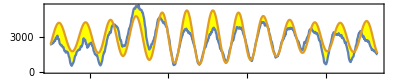

```mathematica
CWF =0.9698; cw[x_] := Sin[CWF*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 1770*cw[i-1.42]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
2*Pi/CWF
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

{char t,7.22158,-14.3409, Years from,1880.17,to,1980.25,CC,36.5647,36.3855,-0.179281}

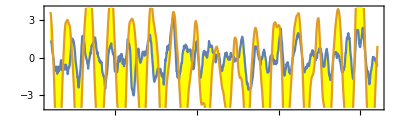

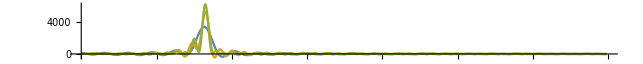

4.36332

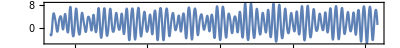

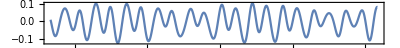

7.27221

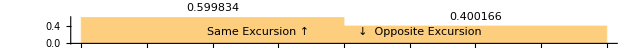

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.05*Sin[0.123*x+0.13])+1.45] ; 
(* CWF =0.9698; cwp[x_] := Sin[CWF*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  *)
tsi[x_]=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.757;  dilate[x_] := -(0.03*Cos[2*Pi*x-0.89]);
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.483;
Hill[x_] := CF*(1-0.19*Cos[CWF*x-.08/CWF]+0.0001*x);
Osc[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.056*Cos[2*Pi/(2*OSC)*x+0.2] - 0.051*Cos[2*Pi*x/(3.0*OSC)-0.6] +.04*Cos[2*Pi*x/(6.0*OSC)-3.9]);
QBOG[x_]:=7.0*qbo[x+0.252]+0.013*Cos[2*Pi*x/(7.0)+0.1]+3.46*Cos[2*Pi*x/(2.33391)-1.51] -1.2*Cos[2*Pi*x/(1.952)-0.98] + 0.37*Cos[2*Pi*x/(2.9)-0.37];
(* CWG[x_]:= If[x<100,0.07*Cos[2*Pi*x/(CWR)+1.0+0.27*Sin[0.524*x-0.3]],0.052*Cos[2*Pi*x/(CWR)+1.7] ]  +0.03*Cos[2*Pi*x/(2*CWR)+2.1];    *)
CWG[x_]:= 0.071*Cos[2*Pi*x/(CWR)+0.000022*x*x+1+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.02*Sin[2*Pi*x/(5.83)-0.3]; (* ,   *)
(* CWG[x_]:=0.1*cw[x+1]; *)
QTO[x_]:= 0.42*Cos[2*Pi*x/(3.801)-1] - 0*0.12*Sin[2*Pi*x/(3.52)-1.4] ;
RHS[x_] :=  0.93*QBOG[x]*(1+0.05*tsi[x-6.8])+CWG[x]+QTO[x]+Osc[x+1.2] + 
           0.043*Cos[2*Pi*x/(18.031)-0.2]+ 0*0.015*Cos[2*Pi*x/(8.85)+0.25]+ 0.4*Cos[2*Pi*x/(1/(1-1/6.483))+0.22] ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.12*(y[x])^2 == 1.03*RHS[x-0.01] ,        y'[TR]==0.0, y[TR]==0.1}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, -1.01*qbo[x+1.03]+First[-2.18*y[x+dilate[x]+0.67] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.3]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.12/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, CWG[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
2*Pi/0.072/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
2
```

2

1.50459

{char t,7.23593,0.037741, Years from,1880.17,to,1980.25,CC,54.3833,59.2548,59.3464,0.0916307}

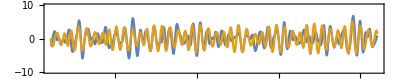

```mathematica
Window1 = 9;  
R = GaussianFilter[GaussianFilter[(1*GaussianFilter[darwin[[All,2]],Window1-0])-(1*GaussianFilter[tahiti[[All,2]],Window1-0]),Window1-2],Window1-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]]  },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.74*RHS[x+0.71]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
2*Pi/.348/12
OldCC = NewCC; NewCC = 50*(1.0-N[Total[SBIN]/Length[SBIN]]) + 50*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
CC = 100*Correlation[lhs,rhs][[2,2]];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",CC, OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
(* missing qbo *)
```

77.5692

{0.,4323.93}

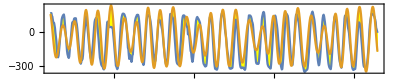

```mathematica
QBOM = Table[{1953.0+x, -47*(0.93*QBOG[72.62+x]+1.*QTO[71.48+x])-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

72.1454

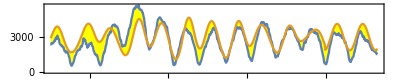

```mathematica
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 16000*CWG[i-1.67]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

```mathematica
1/(1-1/6.483)
```

1.18238

{char t,7.23593,-0.0742329, Years from,1880.17,to,1980.25,CC,77.4242,77.4323,0.0080824}

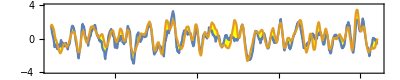

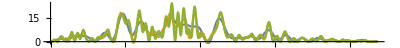

3.37806

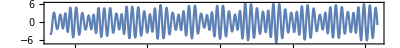

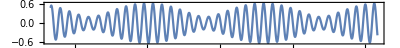

2.25689

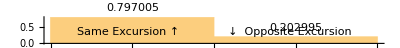

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
tsi[x_]:=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  dilate[x_] := -(0.03*Cos[2*Pi*x-0.89]);
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4825; SEMI := 8.85;
Hill[x_] := CF*(1-0.21*Cos[CWF*x-.08/CWF]+0.0001*x);
Diurnal[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.056*Cos[2*Pi/(2*OSC)*x+0.2] - 0.051*Cos[2*Pi*x/(3.0*OSC)-0.6] +.039*Cos[2*Pi*x/(6.0*OSC)-3.9]);
Semidiurnal[x_] := 0.021*Cos[2*Pi*x/(SEMI)+0.25]-0.1*Cos[2*Pi*x/(SEMI/2)+0.0];
QTO[x_]:= 0.42*Cos[2*Pi*x/(3.801)-1] - 0.22*Sin[2*Pi*x/(3.52)-1.6] ;
QBOG[x_]:=7.0*qbo[x+.252]+.013*Cos[2*Pi*x/7+.1]+3.46*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.071*Cos[2*Pi*x/(CWR)+1.0+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3],
                    0.071*Cos[2*Pi*x/(CWR)+2.0]]  + 0*0.8*Cos[2*Pi*x/(1/(1-1/CWR))+0.32]; (* ,   *)
Saros[x_] := 0.043*Cos[2*Pi*x/(18.031)-0.2];
RHS[x_] := (0.93*QBOG[x]+QTO[x+0.04])*(1+0.05*tsi[x-7])+1.0*CWG[x+0.02]+Diurnal[x+1.2] + Saros[x] + Semidiurnal[x+0.1]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.14*(y[x])^2 == 1.03*RHS[x-0.01] , y'[TR]==-0.001, y[TR]==0.11}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -(1)*qbo[x+1.03]+First[-(1)*2.18*y[x+dilate[x]+0.67] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.155/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, QTO[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
2*Pi/0.232/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

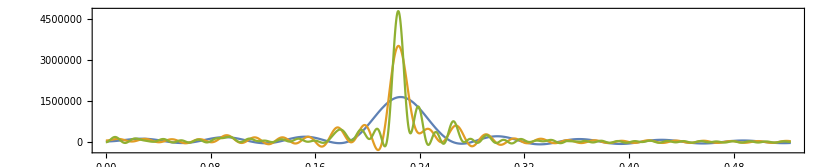

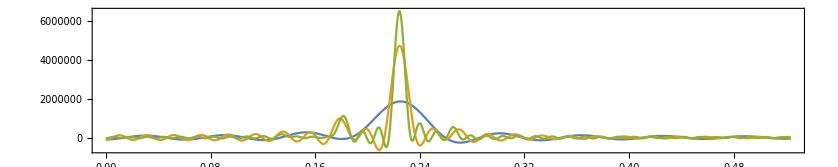

0.137753

0.14875

```mathematica
QBOM = Table[{1953.0+x, -47*(0.93*QBOG[72.62+x]+1.*QTO[71.48+x])-50},{x,1/12,61.25+1/12, 1/12}];  
Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
Plot[Evaluate@Table[PowerSpectralDensity[Q,ω,i],{i,100,500,200}],{ω,0,π/12*2},PlotRange->All,Frame->True,Axes->True,AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[QBOM,ω,i],{i,100,500,200}],{ω,0,π/12*2},PlotRange->All,Frame->True,Axes->True,AspectRatio->0.2] 
2*Pi/3.801/12
2*Pi/3.52/12
```

{char t,4.81898,0.03432, Years from,1880.17,to,1980.25,CC,68.1332,70.2663,2.13319}

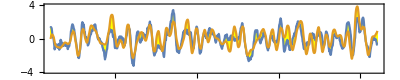

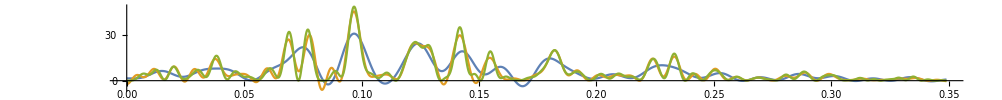

5.51157

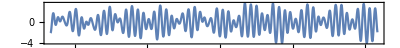

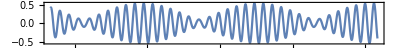

2.25689

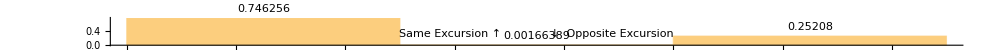

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 5;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
tsi[x_]:=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 1.7;  dilate[x_] := -(0.05*Cos[2*Pi*x-0.8]);
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4825; SEMI := 8.85;
Hill[x_] := CF*(1+0.15*Cos[CWF*x-.0/CWF]+0.0001*x);
Diurnal[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.05*Cos[2*Pi/(2*OSC)*x+0.2] - 0.033*Cos[2*Pi*x/(3.0*OSC)-0.6] +.015*Cos[2*Pi*x/(6.0*OSC)-3.9]);
Semidiurnal[x_] := 0.021*Cos[2*Pi*x/(SEMI)+0.25]-0.08*Cos[2*Pi*x/(SEMI/2)+0.4];
QTO[x_]:= 0.32*Cos[2*Pi*x/(3.8)-0.95] - 0.22*Sin[2*Pi*x/(3.52)-1.2] ;
QBOG[x_]:=3.6*qbo[x+.24]+.014*Cos[2*Pi*x/7+.1]+3.2*Cos[2*Pi*x/2.3339-1.51] -1.2*Cos[2*Pi*x/1.952-.98]-.03*Cos[2*Pi*x/2.9+1.0];
CWG[x_]:= If[x<118, 0.071*Cos[2*Pi*x/(CWR)+1.0+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.08*Sin[2*Pi*x/(5.83)-0.0],
                    0.071*Cos[2*Pi*x/(CWR)+2.0]]  - 0*0.7*Cos[2*Pi*x/(1/(1-1/CWR))+0.32]; (* ,   *)
Saros[x_] := 0.2*Cos[2*Pi*x/(18.031)-0.3];
RHS[x_] := (0.93*QBOG[x]+1.*QTO[x+0.04])-1.5*CWG[x]-0.5*CWG[x/2-1.8]+4.0*Diurnal[x+0.8] + Saros[x] + 0.9*Semidiurnal[x] -0.2*Cos[2*Pi*x/(7.33)+0.5] ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.08*(y[x])^2 == 1*RHS[x-0.05] , y'[TR]==0.1, y[TR]==0.01}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0.0*QBOG[x-0.03]+First[-2*y[x+dilate[x]+0.61] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.095/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, QTO[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
2*Pi/0.232/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```